```mathematica
object=Import[NotebookDirectory[]<>"finish_object.dat"];object=Partition[object,Length[object[[1]]]];Dimensions[object]
```

{17,17,17}

```mathematica
size=Length[object];
radius=(size-1)/2
```

8

```mathematica
density=Partition[Import[NotebookDirectory[]<>"density.dat"],size];Dimensions[density]
```

{17,17,17}

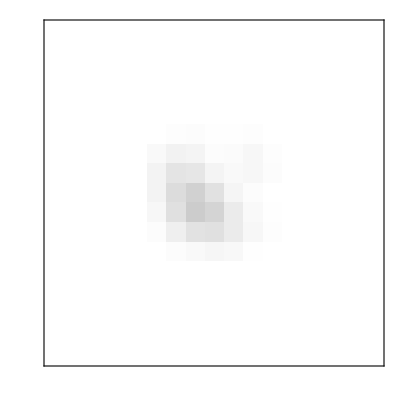
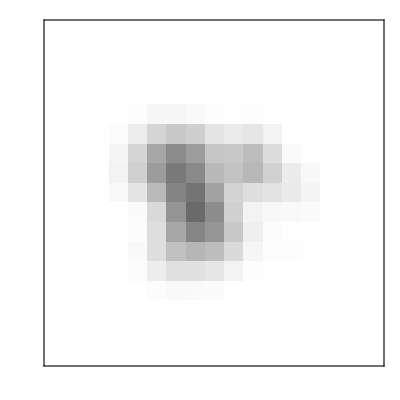
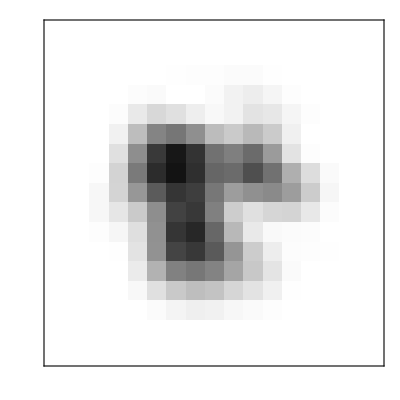
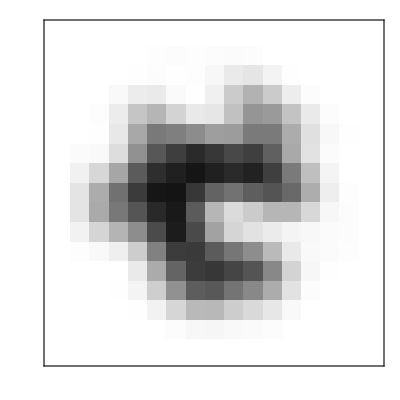
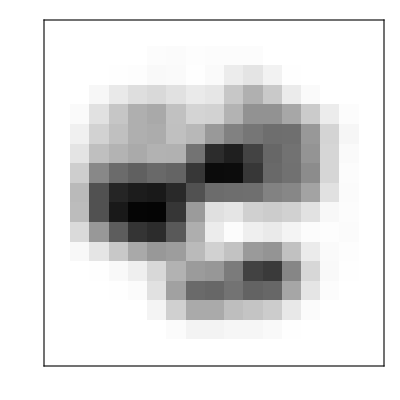
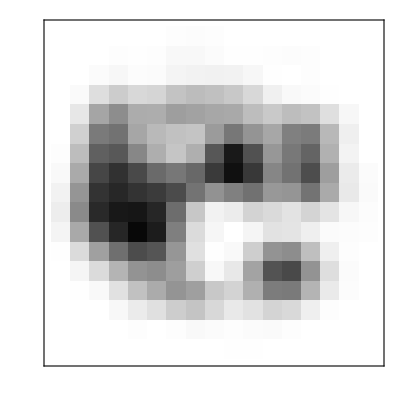
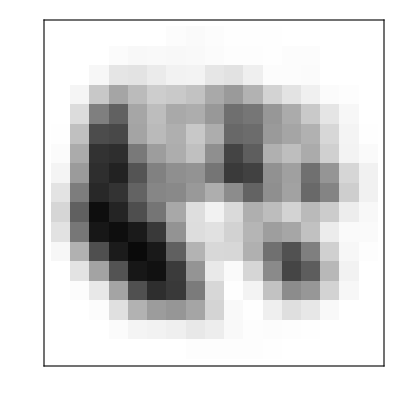
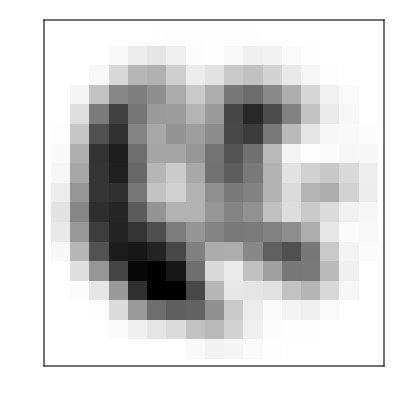

```mathematica
renderStack[object]
```

```mathematica
GraphicsArray[{render3D[object,.5],render3D[density,.5]}]
```

-Graphics-

```mathematica
error=Transpose[Drop[Import[NotebookDirectory[]<>"object.log","Table"],2]][[6]];Length[error]
```

300

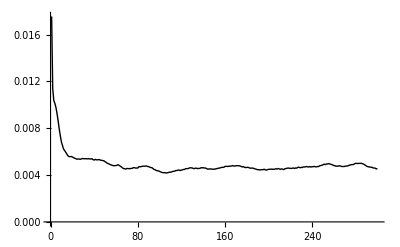

```mathematica
ListPlot[error,Joined->True,PlotRange->{0,Max[error]},PlotStyle->Black]
```

```mathematica
mtf=Select[Import[NotebookDirectory[]<>"mtf.dat"],#[[2]]>0.&];Length[mtf]
```

16

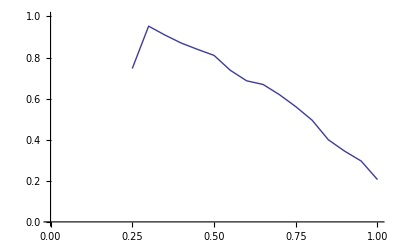

```mathematica
ListPlot[mtf,PlotRange->{{0,1},{0,1}},Joined->True]
```